# PeterBurbery/RecreationalMathematics

This paclet is for recreational mathematics and math puzzles

## Paclet Manifest

"Documentation"

"English"

"Guides"

"MathPuzzles.nb"DocumentationEnglishGuidesMathPuzzles.nb

"ReferencePages"

"Symbols"

"AllBalancedGroupingSymbols.nb"DocumentationEnglishReferencePagesSymbolsAllBalancedGroupingSymbols.nb

"BalancedTernary.nb"DocumentationEnglishReferencePagesSymbolsBalancedTernary.nb

"CatalanUnrank.nb"DocumentationEnglishReferencePagesSymbolsCatalanUnrank.nb

"Derangements.nb"DocumentationEnglishReferencePagesSymbolsDerangements.nb

"DiagonalWalkPlot.nb"DocumentationEnglishReferencePagesSymbolsDiagonalWalkPlot.nb

"DyckPaths.nb"DocumentationEnglishReferencePagesSymbolsDyckPaths.nb

"EulerLinePoints.nb"DocumentationEnglishReferencePagesSymbolsEulerLinePoints.nb

"EvenPermutations.nb"DocumentationEnglishReferencePagesSymbolsEvenPermutations.nb

"FindRegularPolygonTriangulations.nb"DocumentationEnglishReferencePagesSymbolsFindRegularPolygonTriangulations.nb

"FivePointConic.nb"DocumentationEnglishReferencePagesSymbolsFivePointConic.nb

"FullBinaryTrees.nb"DocumentationEnglishReferencePagesSymbolsFullBinaryTrees.nb

"IntegralNumberQ.nb"DocumentationEnglishReferencePagesSymbolsIntegralNumberQ.nb

"Multichoose.nb"DocumentationEnglishReferencePagesSymbolsMultichoose.nb

"NinePointCubic.nb"DocumentationEnglishReferencePagesSymbolsNinePointCubic.nb

"NinePointQuadric.nb"DocumentationEnglishReferencePagesSymbolsNinePointQuadric.nb

"ParenthesizedExpressions.nb"DocumentationEnglishReferencePagesSymbolsParenthesizedExpressions.nb

"PermutationGraph.nb"DocumentationEnglishReferencePagesSymbolsPermutationGraph.nb

"Tutorials"

"Kernel"

"RecreationalMathematics.wl"KernelRecreationalMathematics.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

This paclet contains functions for recreational mathematics and math puzzles.

### Details

I chose a portrait of Leonard Euler for the paclet.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["PeterBurbery`RecreationalMathematics`"];
```

### Basic Examples

Find the form of a conic that runs through five random points:

```mathematica
RandomInteger[1000,{5,2}]
```

{{616,471},{973,581},{266,562},{549,260},{816,423}}

```mathematica
FivePointConic[RandomInteger[1000,{5,2}],{x,y}]
```

1401646447117878700-3765956396643136 x+1032594636108 x^2-5081621649377156 y+8755925322122 x y+3311672803959 y^2

View the symmetric reduction of the five point conic:

```mathematica
SymmetricReduction[1401646447117878700-3765956396643136 x+1032594636108 x^2-5081621649377156 y+8755925322122 x y+3311672803959 y^2,{x,y}]
```

{1401646447117878700+6690736049906 x y-3765956396643136 (x+y)+1032594636108 (x+y)^2,-1315665252734020 y+2279078167851 y^2}

Find a conic section through five points:

```mathematica
p5={{1,4},{4,2},{2,8},{8,5},{5,7}};
conic=FivePointConic[p5,{x,y}]
```

1638-333 x+19 x^2-531 y+36 x y+41 y^2

Show the conic and points:

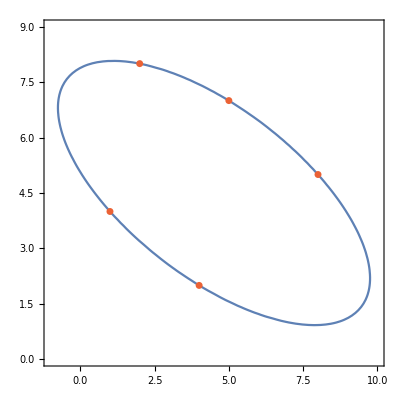

```mathematica
ContourPlot[conic==0,{x,-1,10},{y,0,9},Epilog->{,Point[p5]}]
```

Find a cubic plane curve through nine points:

```mathematica
BlockRandom[SeedRandom[1];
p9=RandomSample[Tuples[Range[-2,2],{2}],9]];
cubic=NinePointCubic[p9,{x,y}]
```

-20-24 x-x^2+3 x^3-28 y+6 x y-2 x^2 y+36 y^2+6 x y^2+24 y^3

Show the cubic and points:

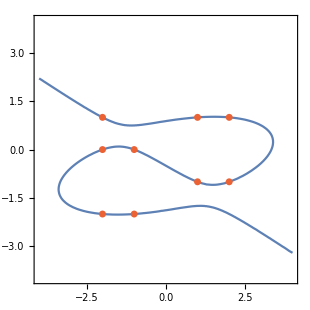

```mathematica
ContourPlot[cubic==0,{x,-4,4},{y,-4,4},Epilog->{,Point[p9]}]
```

Find the defining points for the Euler line of three triangle vertices:

```mathematica
EulerLinePoints[{{-14,-6},{10,-6},{4,12}}]
```

{{-2,0},{0,0},{1,0},{4,0}}

```mathematica
MyFunction[a,b,c]
```

a^2/(b+c)

### Scope

Give more examples showing the range of features in the paclet:

```mathematica
MyPlot[MyFunction[a,3,4],{a,1,10}]
```

-Graphics-

Use screenshots to show features like notebook styles, palettes and external operations:

```mathematica
ViewWebsite["wolframcloud"]
```

-Graphics-

## Source & Additional Information

### Creator

Peter Cullen Burbery

### Source Control Repository

https://github.com/PeterCullenBurbery/recreational-mathematics

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

geometry

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

FivePointConic

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.